```mathematica
ClearAll["Global`*"]

mu[b_,thetaE_]:=((b/thetaE)^2+2)/((b/thetaE)*Sqrt[(b/thetaE)^2+4])
b[x_,y_] = Sqrt[x^2 +y^2] 
mu[ b[3,4], 5]
```

3/(√5)

```mathematica
Manipulate[Plot[mu[b[xx,y],t],{xx,-10,10},AxesLabel->{"bx/ThetaE","Magnification"}],Control[{{y,0.1,"Impact Parameter y component:"},0.1,1,0.1}],Control[{{t,10,"Einstein Angle::"},1,20,1}]]
```

```mathematica
Manipulate[Plot[mu[b[xx,y],t],{xx,-10,10}],{{y,0.1,"y"},0.1,1,0.1},{{t,10,"t"},1,20,1}]
```

```mathematica
Manipulate[Plot[mu[b[xx,y],t],{xx,-10,10}],Control[{{y,0.1,"Impact Parameter y component :"},0.1,1,0.1}],Control[{{t,10,"Einstein Angle:"},1,20,1}]]
```

```mathematica
mu2[ratio_]:=((ratio^2)+2)/(ratio*Sqrt[(ratio)^2+4])
```

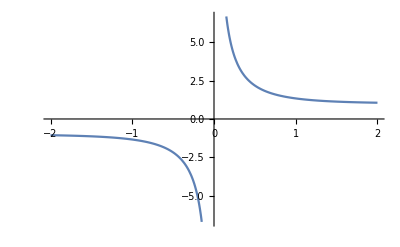

```mathematica
Plot[mu2[ratio], {ratio, -2, 2}]
```

```mathematica
dr=D[ ((ratio^2)+2)/(ratio*Sqrt[(ratio)^2+4]),ratio ]
```

-(2+ratio^2)/((4+ratio^2)^(3/2))+2/(√(4+ratio^2))-(2+ratio^2)/(ratio^2 √(4+ratio^2))

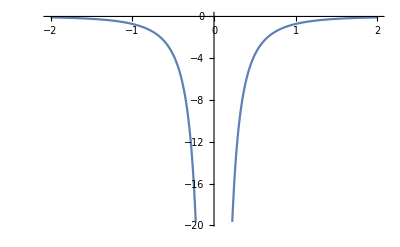

```mathematica
Plot[dr, {ratio, -2, 2}]
```

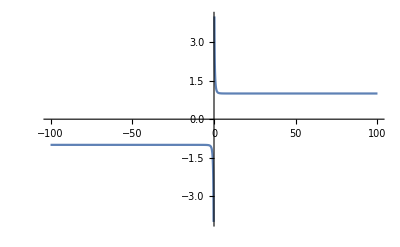

```mathematica
Plot[mu2[ratio], {ratio, -100, 100}]
```

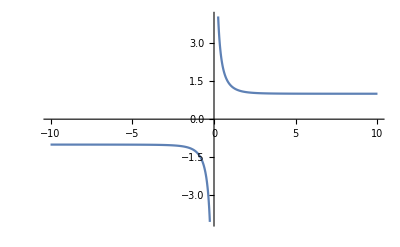

```mathematica
Plot[mu2[ratio], {ratio, -10, 10}]
```

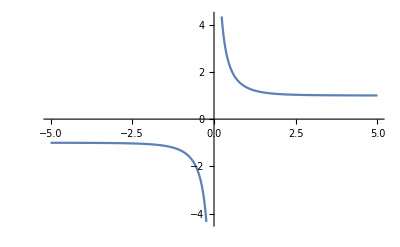

```mathematica
Plot[mu2[ratio], {ratio, -5, 5}]
```

```mathematica
Manipulate[Plot[mu[bx,thetaE],{bx,-10,10},PlotRange->All],{thetaE,0.1,10,Appearance->"Labeled"}]
```